```mathematica
<<VisualDebug`
```

## first attempt

```mathematica
expr=Hold[{2+3,5^2,9+0}];
stringExpr=FullForm[expr]//ToString;
length=StringLength[stringExpr];
Manipulate[
startString=StringTake[stringExpr,{1,startPos-1}];
midString=StringTake[stringExpr,{startPos, endPos}];
endString=StringTake[stringExpr,{endPos+1,length}];
Row[{startString,Style[midString,FontColor->ColorData["Rainbow"][0.5]],endString}];
Row[{Style[Extract[expr,mainPart,HoldForm],FontColor->ColorData["Rainbow"][0.5]]}],

{startPos,1,endPos,1,Appearance->"Labeled"},
{{endPos,length},startPos, length,1,Appearance->"Labeled"},
{mainPart,0, Length[expr],1}
]
```

## shape function (depricated)

```mathematica
StringLength["Abc"]
```

3

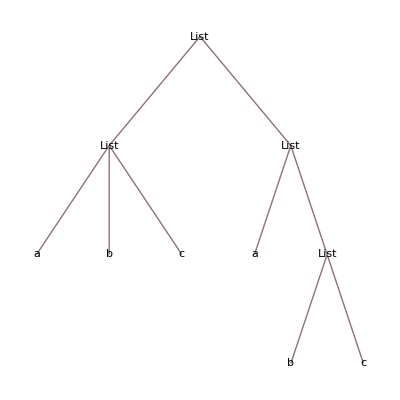

```mathematica
{{a,b,c},{a,{b,c}}}//TreeForm
```

```mathematica
a->0
{a}->1
{a,b}->{2,{0,0}}
shape@{{a,d},{b,c}}
```

a→0

{a}→1

{a,b}→{2,{0,0}}

shape[{{a,d},{b,c}}]

```mathematica
Depth[HoldForm[a]]
```

2

```mathematica
Remove[shape]
SetAttributes[shape,HoldAll]
shape[expr_]:=Module[
{

},
If[Depth[Unevaluated[expr]]==1,
Return[0],
Return[{Length[Unevaluated[expr]],shape@@@(Map[Unevaluated,ReplacePart[Hold[expr],{1,0}->List],{2}]//ReleaseHold)}]
]
]
```

```mathematica
expr1=Hold[2+2+Integrate[x^6+3,{x,0,2}]]
sh=shape[2+2+Integrate[x^6+3,{x,0,2}]]
Position[%,_List]
Extract[expr1,{1,3,1,1,2}]
```

Hold[2+2+∫_0^2 (x^6+3)ⅆx]

{3,{0,0,{2,{{2,{{2,{0,0}},0}},{3,{0,0,0}}}}}}

{{2,3,2,1,2,1,2},{2,3,2,1,2,1},{2,3,2,1,2},{2,3,2,1},{2,3,2,2,2},{2,3,2,2},{2,3,2},{2,3},{2},{}}

6

## debug function

```mathematica
expr1=Hold[2+2+Integrate[x^6+3,{x,0,2}]];
debug[expr1, Heads -> False]
```

## My step function

```mathematica
Remove[step]
<<VisualDebug`
```

```mathematica
s[x_]:=Exp[x]
f[x_]:=k[x]
k[x_]:=x-2
g[x_]:=Sin[x]
h[x_]:=x^2
```

```mathematica
step[s[f[g[h[4]]]]]
step[s[f[g[16]]]]
step[s[f[Sin[16]]]]
step[s[k[Sin[16]]]]
```

s[f[g[16]]]

s[f[Sin[16]]]

s[k[Sin[16]]]

s[-2+Sin[16]]

```mathematica
expr=Unevaluated[2+3^4]
stepTrace[2+3^4]
```

83

{2+3^4,2+81,83}

```mathematica
k=2
Head[Unevaluated[k]]
```

2

Symbol

```mathematica
stepTrace[s[f[g[h[4]]]]]
```

{s[f[g[h[4]]]],s[f[g[16]]],s[f[Sin[16]]],s[k[Sin[16]]],s[-2+Sin[16]],ⅇ^(-2+Sin[16])}

## A step test

```mathematica
<<VisualDebug`
Integrate[x+x,{x,0,1}]
```

1

```mathematica
step[Integrate[x+x, {x, 0, 1}]]
step[Integrate[2x, {x, 0, 1}]]
```

∫_0^1 2 xⅆx

1

```mathematica
stepTrace[Integrate[x+x, {x, 0, 1}]]
stepTracePrint[Integrate[x+x, {x, 0, 1}]]
```

{∫_0^1 (x+x)ⅆx,∫_0^1 2 xⅆx,1}

∫_0^1 (x+x)ⅆx

∫_0^1 2 xⅆx

1

```mathematica
stepTracePrint[]
```

stepTracePrint[]